# Reference count: pubyear: 1946 - 2020

MIS41の準備

## Setting

```mathematica
workdir="/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/

```mathematica
filelisttxt="/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/reflist_filenames.txt"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/reflist_filenames.txt

```mathematica
filelist=StringSplit[Import[filelisttxt,"String"]]
```

{reflistBypubyear_163-167.wl,reflistBypubyear_168-172.wl,reflistBypubyear_173-177.wl,reflistBypubyear_178-182.wl,reflistBypubyear_183-187.wl,reflistBypubyear_188-192.wl,reflistBypubyear_193-197.wl,reflistBypubyear_198-202.wl,reflistBypubyear_203-207.wl,reflistBypubyear_208-212.wl,reflistBypubyear_213-217.wl,reflistBypubyear_218-222.wl,reflistBypubyear_223-227.wl,reflistBypubyear_228-232.wl,reflistBypubyear_233-237.wl}

```mathematica
timespan="1946-2020"
```

1946-2020

対象データ：
1946-2020年に出版された論文（およそ3000万件）のレファレンス（PMID vs. PMID）のうち上位1000件（3万分の1）

## Import（3回目以降skip）

```mathematica
SetDirectory[workdir]
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference

reference count : citing -> cited

この量になると読み込みに2~3 分かかる。

```mathematica
Timing[(e[2020]=Flatten[Map[Get[#]&,filelist[[1;;15]]]])//Length]
```

{92.4195,223840771}

```mathematica
Timing[eg[2020,"cited"]=GroupBy[e[2020],Last];]
```

{135.818,Null}

## Count ref edge by citing(cited)（2回目以降skip）

セレクションのため、一旦エッジ（レファレンス）をカウントする。

reference count

```mathematica
e[2020,"reference count"]=e[2020]//Length
```

223840771

citing article count

```mathematica
(*(e[1960,"citing art count"]=Sort[Tally[e[1960],#1[[1]]==#2[[1]]&],#1[[2]]>=#2[[2]]&])//Length*)
```

```mathematica
Timing[(e[2020,"citing art count"]=SortBy[Tally[e[2020],#1[[1]]==#2[[1]]&],-#[[2]]&])//Length]
```

{85.8608,6872207}

cited article count

```mathematica
(*(e[1960,"cited art count"]=Sort[Tally[e[1960],#1[[2]]==#2[[2]]&],#1[[2]]>=#2[[2]]&])//Length*)
```

```mathematica
Timing[(e[2020,"cited art count"]=SortBy[Tally[e[2020],#1[[2]]==#2[[2]]&],-#[[2]]&])//Length]
```

{368.202,18880844}

```mathematica
Save[workdir<>"1946-2020-edge-count_CitingOrCitedGather.save",e]
```

## Rank stat & selection（3回目以降skip）

順位による範囲

### Q1-Q4範囲

```mathematica
Timing[Get[workdir<>"1946-2020-edge-count_CitingOrCitedGather.save"];]
```

{112.871,Null}

Quantileを設計する。: 4分してそれぞれの上位を掬う。各1000とする。

```mathematica
Length[e[2020,"cited art count"]]
```

18880844

```mathematica
span=Length[e[2020,"cited art count"]]/4//N
```

4.72021×10^6

```mathematica
spanStart=Ceiling[Table[n span,{n,0,3}]+1]
```

{1,4720212,9440423,14160634}

```mathematica
spanStop=spanStart+999
```

{1000,4721211,9441422,14161633}

```mathematica
(*Save[workdir<>"mis41-sel-Q1Q4-span.save",{spanStart,spanStop}]*)
```

### Q1

対象となるPMIDの抽出

```mathematica
Q1[1000]=Map[#[[1,2]]&,e[2020,"cited art count"][[spanStart[[1]];;spanStop[[1]]]]];
```

```mathematica
(Q1refs[1000]=Map[eg[2020,"cited"][#]&,Q1[1000]])//Length
```

1000

```mathematica
Map[Length,Q1refs[1000]]
```

{54249,53050,47343,44350,27998,26196,23032,22517,18449,18152,16282,15705,14250,13930,13533,13523,13449,13435,13318,13202,13016,12950,12906,12418,12151,12038,12009,11911,11896,11884,11520,11338,11217,11169,11146,11117,11001,10863,10847,10590,10447,10424,10321,10284,10013,9769,9687,9614,9543,9470,9397,9355,9279,9110,9098,8781,8775,8772,8507,8481,8278,8203,8187,8103,8084,8058,8044,8013,7784,7743,7600,7525,7523,7490,7480,7479,7468,7340,7319,6956,6923,6909,6879,6735,6674,6614,6535,6499,6461,6454,6451,6426,6411,6408,6396,6373,6275,6251,6244,6242,6211,6186,6181,6170,6122,6120,6113,6096,6076,6037,6011,5992,5927,5921,5894,5892,5869,5862,5852,5820,5760,5742,5730,5724,5724,5714,5685,5649,5640,5633,5629,5600,5596,5588,5582,5581,5557,5555,5537,5526,5525,5523,5512,5510,5500,5445,5412,5412,5352,5332,5302,5299,5271,5236,5228,5191,5134,5115,5102,5100,5061,5020,5002,4922,4900,4881,4853,4852,4847,4838,4828,4828,4827,4827,4808,4805,4799,4780,4763,4756,4753,4742,4694,4689,4669,4666,4662,4645,4632,4602,4600,4597,4590,4588,4577,4506,4467,4466,4464,4460,4457,4457,4444,4432,4425,4422,4419,4416,4409,4401,4388,4386,4374,4342,4339,4333,4320,4299,4287,4282,4240,4240,4224,4222,4209,4208,4203,4193,4183,4183,4182,4181,4177,4131,4110,4106,4099,4097,4095,4085,4077,4060,4058,4057,4052,4051,4049,4045,4043,4039,4021,4020,4015,4011,4010,4010,3999,3986,3969,3943,3935,3929,3902,3898,3896,3892,3891,3876,3856,3854,3849,3836,3832,3829,3825,3810,3810,3793,3782,3778,3775,3742,3737,3736,3731,3726,3726,3714,3694,3693,3684,3675,3668,3653,3629,3628,3612,3608,3607,3603,3603,3601,3591,3587,3576,3575,3566,3524,3504,3503,3503,3497,3486,3484,3483,3475,3472,3469,3469,3463,3455,3448,3441,3437,3434,3423,3422,3422,3418,3398,3391,3373,3370,3362,3343,3327,3319,3312,3305,3300,3293,3292,3284,3275,3272,3272,3269,3267,3266,3258,3255,3252,3248,3246,3245,3241,3236,3235,3235,3229,3220,3214,3204,3202,3198,3193,3179,3174,3173,3171,3165,3161,3155,3155,3153,3144,3128,3123,3120,3104,3098,3096,3094,3092,3091,3074,3068,3064,3063,3062,3053,3052,3048,3046,3041,3038,3032,3019,3008,3004,3002,2998,2997,2996,2988,2983,2981,2970,2966,2958,2954,2953,2949,2945,2943,2938,2933,2931,2928,2922,2920,2916,2910,2909,2908,2908,2903,2897,2891,2891,2890,2883,2883,2875,2874,2872,2864,2864,2861,2854,2852,2849,2846,2841,2840,2838,2838,2835,2833,2831,2827,2812,2807,2805,2804,2798,2783,2782,2771,2768,2764,2761,2761,2760,2756,2755,2743,2736,2734,2734,2734,2730,2729,2725,2723,2722,2721,2720,2719,2712,2708,2690,2685,2683,2683,2682,2679,2676,2659,2655,2651,2650,2643,2639,2637,2636,2631,2631,2620,2618,2616,2614,2613,2607,2607,2606,2602,2602,2594,2594,2593,2590,2587,2582,2576,2575,2575,2574,2573,2571,2563,2563,2552,2549,2544,2539,2534,2528,2523,2523,2521,2521,2514,2510,2510,2506,2506,2505,2500,2498,2496,2494,2494,2493,2486,2483,2481,2479,2478,2476,2473,2472,2470,2469,2466,2460,2460,2459,2458,2456,2455,2454,2454,2454,2453,2452,2449,2446,2443,2438,2436,2432,2431,2430,2428,2428,2425,2424,2423,2416,2414,2411,2410,2406,2404,2403,2403,2402,2397,2394,2391,2390,2389,2388,2386,2381,2377,2376,2373,2373,2372,2370,2367,2364,2363,2362,2359,2358,2358,2354,2354,2351,2351,2350,2346,2344,2341,2340,2340,2339,2329,2329,2326,2326,2320,2320,2319,2309,2306,2305,2305,2304,2304,2299,2299,2297,2297,2294,2292,2290,2289,2287,2283,2282,2282,2280,2279,2278,2277,2277,2275,2274,2270,2261,2260,2259,2258,2258,2256,2253,2252,2250,2248,2246,2241,2240,2239,2238,2236,2236,2233,2233,2231,2223,2220,2219,2217,2215,2215,2210,2209,2209,2206,2206,2205,2205,2201,2199,2198,2198,2198,2197,2197,2197,2196,2195,2194,2194,2191,2188,2185,2184,2182,2182,2182,2180,2180,2175,2175,2173,2170,2169,2168,2167,2164,2163,2163,2162,2161,2161,2156,2155,2155,2153,2152,2152,2151,2150,2144,2142,2142,2140,2138,2137,2136,2135,2135,2134,2127,2127,2124,2122,2122,2121,2121,2117,2114,2113,2112,2112,2112,2111,2109,2108,2107,2106,2101,2101,2098,2097,2096,2096,2094,2093,2093,2090,2090,2089,2088,2083,2077,2076,2071,2070,2069,2067,2067,2066,2063,2063,2060,2060,2060,2058,2056,2055,2053,2051,2050,2050,2050,2049,2047,2045,2044,2041,2041,2041,2037,2036,2034,2033,2031,2027,2021,2017,2015,2015,2014,2010,2007,2007,2006,2006,2003,2001,1998,1995,1994,1992,1992,1991,1991,1989,1985,1982,1980,1979,1977,1977,1976,1970,1970,1968,1968,1967,1967,1967,1964,1962,1962,1961,1961,1958,1957,1951,1948,1947,1947,1947,1946,1945,1944,1944,1944,1942,1941,1940,1939,1939,1939,1938,1935,1935,1930,1924,1924,1922,1920,1919,1919,1919,1913,1913,1911,1911,1908,1907,1906,1904,1897,1897,1897,1895,1893,1890,1890,1890,1890,1888,1888,1888,1886,1886,1886,1886,1884,1884,1883,1882,1879,1877,1876,1876,1876,1875,1874,1874,1873,1873,1873,1872,1872,1871,1871,1870,1870,1869,1865,1864,1864,1862,1862,1860,1859,1859,1858,1857,1857,1857,1856,1855,1854,1851,1850,1849,1849,1848,1848,1847,1844,1844,1843,1843,1840,1839,1838,1838,1837,1835,1833,1832,1831,1830,1829,1829,1826,1822,1822,1822,1821,1820,1819,1816,1816,1815,1814,1813,1812,1812,1809,1809,1807,1806,1806,1806,1805,1805,1804,1803,1803,1802,1802,1801,1800,1800,1799,1799,1797,1797,1796,1796,1794,1792,1791,1790,1789,1789,1786,1785}

```mathematica
Mean[Map[Length,Q1refs[1000]]]//N
```

3789.24

### Q2

対象となるPMIDの抽出

```mathematica
Q2[1000]=Map[#[[1,2]]&,e[2020,"cited art count"][[spanStart[[2]];;spanStop[[2]]]]];
```

```mathematica
(Q2refs[1000]=Map[eg[2020,"cited"][#]&,Q2[1000]])//Length
```

1000

```mathematica
Map[Length,Q2refs[1000]]
```

{11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11}

### Q3

対象となるPMIDの抽出

```mathematica
Q3[1000]=Map[#[[1,2]]&,e[2020,"cited art count"][[spanStart[[3]];;spanStop[[3]]]]];
```

```mathematica
(Q3refs[1000]=Map[eg[2020,"cited"][#]&,Q3[1000]])//Length
```

1000

```mathematica
Map[Length,Q3refs[1000]]
```

{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

### Q4

対象となるPMIDの抽出

```mathematica
Q4[1000]=Map[#[[1,2]]&,e[2020,"cited art count"][[spanStart[[4]];;spanStop[[4]]]]];
```

```mathematica
(Q4refs[1000]=Map[eg[2020,"cited"][#]&,Q4[1000]])//Length
```

1000

```mathematica
Map[Length,Q4refs[1000]]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

### Save

```mathematica
(*Save[workdir<>"mis41-sel-Q1Q4-ref.save",{Q1refs,Q2refs,Q3refs,Q4refs}]*)
```

## Analysis

### 分析ベース

プログラムのロード：

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/PMIDtoPubyear.wl"];
```

```mathematica
addZeroTally[data_,start_,end_]:=Module[{li,add},
li=Map[#[[1]]&,data];
add=Map[{#,0}&,Complement[Range[start,end],li]];
Join[add,data]//Sort
]
```

```mathematica
splitAtYear[list_,year_]:=Module[{pos=1},
pos=Position[list,year][[1,1]];
If[pos=={},pos=1];
If[pos==1,{{},list},TakeList[list,{pos-1,All}]]
]
```

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/coldef.wl"];
```

```mathematica
myColor1[z_]:=RGBColor[z,0.8(1-z),0.4(1-z)];
myColor2[z_]:=CMYKColor[z,((1-z)/3)^2,((1-z)/2)^2,Sqrt[z]];
myColor3[z_]:=CMYKColor[((1-z)/3)^2,z,((1-z)/2)^2,Sqrt[z]];
myColor4[z_]:=CMYKColor[((1-z)/3)^2,((1-z)/3)^2,z,Sqrt[z]];
myColor5[z_]:=CMYKColor[(z)^2,(z),(z),(z)^(1.2)];
myColor6[z_]:=Blend[{Red,Green,White},{1,0.75(1-z),(1-z)^(3)}];
cf1=Function[{x,y,z},Hue[5/6 (1-z),0.3+(z^2),1]];
cf2=Function[{x,y,z},Hue[5/6 (1-z),#+(1-#)*z,1]&@0.05];
cf3=Function[{x,y,z},Hue[5/6*(1-z),(#1+(1-#1)*z)^#2,1]]&@@{.25(*offset*),1.0(*gain*)};
```

データのロード：

```mathematica
len=1000
```

1000

```mathematica
Get[workdir<>"mis41-sel-Q1Q4-ref.save"];
```

データの整形：

```mathematica
Q1refyears=ToExpression[Map[PMIDtoPubyear[#[[1]]]&,Q1refs[1000],{2}]];
```

```mathematica
Q1pubyear=ToExpression[Map[PMIDtoPubyear[#[[1,2]]]&,Q1refs[1000]]];
```

```mathematica
Q1PMID=Map[#[[1,2]]&,Q1refs[1000]];
```

時系列の範囲を設定する：

```mathematica
Flatten[Q1refyears]//Max
Flatten[Q1refyears]//Min
Q1pubyear//Max
Q1pubyear//Min
```

2020

1951

2020

1949

```mathematica
startYear=1949
endYear=2020
```

1949

2020

各種時系列データを作る：

引用がある年の引用数：

```mathematica
Q1refyearsTally=Map[Tally,Q1refyears];
```

調査期間すべてでゼロパディングしたデータ：

```mathematica
(Q1refyearsTallyFull=Map[addZeroTally[#,startYear,endYear]&,Q1refyearsTally])//Dimensions
```

{1000,72,2}

出版年から2020までのデータ：

```mathematica
Q1refyearsTallyPY=Table[splitAtYear[Q1refyearsTallyFull[[n]],Q1pubyear[[n]]][[2]],{n,1,len}];
```

年齢が若い順のオーダー：

```mathematica
odr=Ordering[Map[Length,Q1refyearsTallyPY]];
```

出版年からの被引用数カウント：

```mathematica
(Q1refyearsTallyPYcount=Map[#[[2]]&,Q1refyearsTallyPY,{2}])//Dimensions
```

{1000}

```mathematica
ListLinePlot3D[Q1refyearsTallyPYcount[[odr//Reverse]],PlotRange->Full,ColorFunction->myColor2]
```

-Graphics3D-

### オブソレッセンス

モデル：

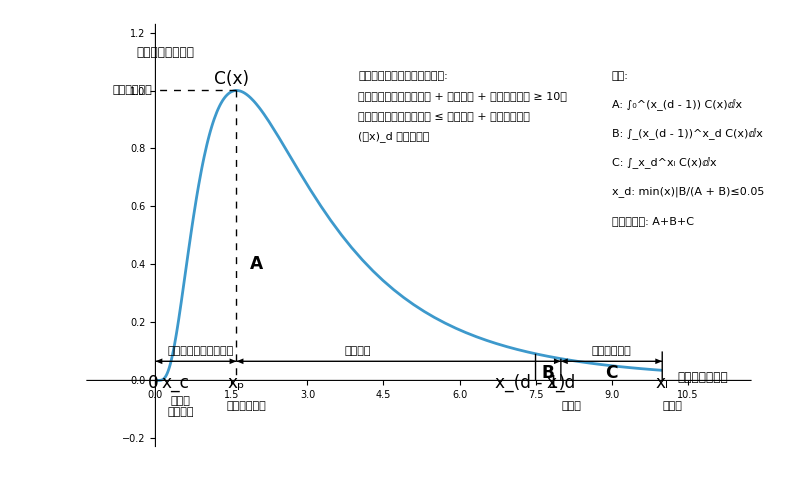

指標値定義：

```mathematica
acRatio[l_]:=Module[{ac},
ac=Accumulate[l];
N[l/ac]/.Indeterminate->1
]
```

```mathematica
ndiff[l_,w_]:=BlockMap[(#[[-1]]-#[[1]])/(w-1)&,Join[Table[0,{w-1}],l],w,1]
```

```mathematica
ndiff[l_]:=BlockMap[(#[[-1]]-#[[1]])&,l,2,1]
```

```mathematica
myVar[l_]:=If[Length[l]>1,Variance[l],0]
```

```mathematica
basicStat[citedcount_]:=Module[{len,argPeak,peakYear,max,decsustainPeriod,decayTH,decayPlist,decayCited,decayPeriod,firstCitedYear,total,Av5year,diff,diff2,diffTotal},
decayTH=0.05;
len=Length[citedcount];
argPeak=Flatten[Position[citedcount,max=Max[citedcount]]];
peakYear=argPeak[[1]];
decsustainPeriod=len-argPeak[[-1]];
decayPlist=Cases[Flatten[Position[acRatio[citedcount],x_/;x<=decayTH]],x_/;x>peakYear];
decayCited=Total[citedcount[[;;Min[decayPlist]]]];
decayPeriod=Min[decayPlist]-peakYear;
If[Length[decayPlist]<=0,decayPeriod="InDecay"];
firstCitedYear=Min[Position[citedcount,x_/;x>0]]-1;
total=Total[citedcount];
Av5year=MovingAverage[Join[citedcount,Table[0,{n,4}]],5];
diff=ndiff[Av5year];
diff2=ndiff[diff];
diffTotal=Total[diff//N];
Association[{"len"->len,"peakYear"->peakYear,"peakCount"->max,"peakRatio"->max/decayCited//N,"peakPosition"->peakYear/Min[decayPlist]//N,"decay-sustainPeriod"->decsustainPeriod,"decayCited"->decayCited,"decayPeriod"->decayPeriod,"firstCitedYear"->firstCitedYear,"totalCited"->total,"V:Av5year"->myVar[Av5year//N],"V:diff"->myVar[diff//N],"V:diff2"->myVar[diff2//N],"diffTotal"->diffTotal,"diffSeq"->diff}]
]
```

各値の説明：

"len" = > 出版から2020までの年数
"peakYear" = > 出版からピークを迎えるまでの年数☑️
"peakCount" = > ピークの年の被引用数☑️
"peakRatio" = > peakCount/decayCited （"活動期間" の被引用）
"peakPosition" = > "活動期間" 中におけるpeakの位置 （全体を1とする）
"sustainYear" = > ピークの年から2020までの年数
"decayYear" = > ピークの年を超えてから年間引用が全体の引用の5 % 以下となるまでの出版からの年数☑️
"decayCited" = > decayYearまでの被引用数☑️
"firstCitedYear" = > 最初の引用が発生するまでの年数 （出版年に発生すると0）
"totalCited" = > 出版年から2020までの総被引用数
"V:Av5year" = > 5 年引用数平均の分散（ゼロパディングあり）☑️
"V:diff" = > 5 年引用数平均の差分の分散 ☑️
"V:diff2" = > 5 年引用数平均の差分の差分の分散☑️
"diffTotal" = > 5 年引用数平均の差分の累計：十分に大きい値があり十分に長い期間があれば0に近づく

```mathematica
(Q1refyearsBasicstat=Map[basicStat,Q1refyearsTallyPYcount])//Dimensions
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

Part::span: 1;;∞は有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

Power::infy: 無限式1/0が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

Part::span: 1;;∞は有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

General::stop: この計算中に，Part::spanのこれ以上の出力は表示されません．

{1000}

判定基準：

・出版から十分な時間が経過している：”len”が十分に長い(10年以上)
・ピーク期が十分に過ぎ去っている：“decay-sustainPeriod”が“peakYear”以上
・被引用の傾向が十分に低下している：“diffTotal”が”totalCited”に比べて十分に小さい(5%以下)

```mathematica
(Q1obsolatedPos=Flatten[Position[Q1refyearsBasicstat,x_/;x["len"]>=10&&x["decay-sustainPeriod"]>=x["peakYear"]&&(x["diffTotal"]/x["totalCited"])<=0.05]])//Length
```

Total::normal: Total[len]で1の位置に原子的ではない式が想定されます．

Total::normal: Total[decay-sustainPeriod]で1の位置に原子的ではない式が想定されます．

Total::normal: Total[peakYear]で1の位置に原子的ではない式が想定されます．

General::stop: この計算中に，Total::normalのこれ以上の出力は表示されません．

Infinity::indet: 不定式0 DirectedInfinity[diffTotal]が見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

142

セレクション：

```mathematica
Q1refyearsTallyPYcountOBS=Q1refyearsTallyPYcount[[Q1obsolatedPos]];
Q1refyearsOBS=Q1refyears[[Q1obsolatedPos]];
Q1pubyearOBS=Q1pubyear[[Q1obsolatedPos]];
Q1PMIDOBS=Q1PMID[[Q1obsolatedPos]];
```

```mathematica
odrOBS=Ordering[Map[Length,Q1refyearsTallyPYcountOBS]];
```

```mathematica
ListLinePlot3D[Q1refyearsTallyPYcountOBS[[odrOBS//Reverse]],PlotRange->Full,ColorFunction->myColor2]
```

-Graphics3D-

### 統計

1000件：出版から最大被引用年までの期間

```mathematica
Q1All["peakYear"]=Map[#["peakYear"]&,Q1refyearsBasicstat]
Q1All["decayPeriod"]=Map[#["decayPeriod"]&,Q1refyearsBasicstat]
```

{23,28,20,44,4,31,16,15,10,46,18,12,12,5,12,11,18,12,8,21,16,10,17,4,3,9,34,24,12,17,7,4,17,13,4,9,44,34,12,9,29,17,7,64,18,11,10,10,7,35,5,25,9,11,44,11,62,16,21,4,28,5,1,38,9,9,38,31,8,11,20,17,11,19,4,12,21,19,13,8,14,8,2,12,20,12,9,10,16,11,34,7,7,6,7,15,2,5,36,35,13,14,11,18,43,10,5,8,8,8,9,11,12,14,9,12,4,10,10,25,61,12,8,43,23,2,2,6,3,2,11,16,58,11,12,6,9,32,23,1,2,10,28,15,10,10,24,14,21,9,5,10,12,12,11,19,2,14,12,13,7,7,10,10,10,13,29,1,11,10,10,1,16,14,7,38,22,21,5,19,16,21,9,12,41,9,9,19,15,12,17,7,15,10,33,25,33,24,9,19,5,1,19,33,12,23,12,8,8,2,6,16,13,25,10,13,16,16,16,14,14,8,6,7,17,20,30,25,30,6,4,9,2,9,1,10,20,34,17,11,65,12,12,2,3,67,12,10,12,15,42,9,8,19,7,40,18,9,14,8,14,21,35,56,17,6,4,10,19,13,11,13,12,16,14,8,9,6,4,4,31,14,8,9,14,14,10,16,26,11,15,8,8,16,10,31,34,11,9,18,11,5,12,19,6,12,14,72,19,9,17,12,13,19,62,39,21,12,12,11,27,13,22,14,11,5,6,9,18,30,15,26,6,6,15,15,12,15,19,8,17,22,10,4,6,1,1,4,10,15,43,7,15,37,4,13,6,7,52,9,16,9,15,5,10,13,10,9,8,9,13,9,11,58,5,11,6,28,40,26,5,6,31,11,37,24,18,28,6,47,27,12,4,5,7,24,13,15,12,6,21,1,6,10,38,5,3,15,5,20,8,9,7,8,12,12,6,18,10,28,11,19,12,8,13,9,21,12,6,28,23,13,5,15,12,8,2,10,29,13,20,11,15,8,9,12,10,13,10,23,12,11,6,15,10,12,9,17,40,11,14,11,9,13,10,17,6,5,21,5,9,6,11,11,4,7,64,15,39,15,14,22,5,14,2,8,5,10,1,15,22,21,17,10,39,8,29,11,8,16,16,13,3,12,10,12,17,6,17,6,5,9,21,14,10,8,11,15,8,8,12,30,17,9,47,16,12,17,12,8,10,11,56,4,10,22,42,17,31,19,17,25,5,14,55,6,14,16,42,6,17,12,11,8,41,14,13,15,21,11,26,12,27,13,5,14,10,6,9,14,8,6,2,4,11,35,12,8,19,3,12,16,5,24,26,17,6,12,17,17,11,6,22,12,8,12,28,4,12,39,11,2,3,16,19,20,14,6,25,9,8,11,17,15,8,18,18,13,5,19,12,54,9,25,17,10,12,14,11,5,4,21,10,22,7,9,16,27,19,34,14,46,9,12,9,16,27,12,7,15,7,10,26,5,6,22,16,12,40,7,28,14,9,22,23,1,13,23,12,24,10,26,16,7,2,5,4,11,7,24,15,10,3,21,14,3,7,33,12,16,17,7,6,26,4,22,16,21,16,18,16,21,14,6,6,40,8,21,4,17,15,7,19,12,14,12,12,21,18,33,12,26,58,9,9,7,5,8,5,13,5,20,18,14,10,13,12,8,17,9,18,38,23,71,30,8,15,7,10,12,17,53,6,15,14,5,11,8,8,8,9,1,10,15,3,11,8,13,4,4,15,9,12,36,10,13,44,13,31,18,2,7,3,25,8,28,43,9,30,8,26,15,16,26,12,16,10,8,15,6,14,15,16,11,5,4,47,19,6,17,11,5,10,9,8,6,25,29,12,10,18,17,10,6,21,12,26,3,8,35,21,9,15,13,39,12,32,28,12,13,12,16,12,10,12,11,5,11,68,17,9,6,15,15,9,40,10,6,10,10,11,4,20,20,12,23,1,16,13,7,6,10,3,9,9,10,17,13,9,17,8,10,7,2,7,18,11,10,20,14,14,12,18,4,2,8,11,14,4,5,22,7,19,10,7,12,11,32,9,6,1,7,17,17,6,11,9,15,6,10,6,10,10,3,18,1,18,18,11,10,3,9,4,30,10,10,22,11,8,5,12,11,6,6,3,49,14,6,11,6,13,12,6,16,14,9,15,7,9,8,6,25,13,12,8,12,12,65,17,9,12,18,9,12,9,24,26,8,16,6,22,22,12,7,19,6,12,3,31,6,9,26,31,12,13,43,7,11,21,13}

{5,10,InDecay,1,5,InDecay,6,6,InDecay,InDecay,5,InDecay,InDecay,InDecay,InDecay,8,InDecay,InDecay,InDecay,InDecay,InDecay,6,InDecay,6,InDecay,InDecay,InDecay,InDecay,7,6,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,5,InDecay,InDecay,InDecay,5,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,5,InDecay,InDecay,4,InDecay,InDecay,InDecay,InDecay,7,9,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,6,InDecay,6,InDecay,6,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,8,11,6,InDecay,InDecay,InDecay,InDecay,InDecay,6,InDecay,5,InDecay,7,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,6,InDecay,InDecay,6,InDecay,7,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,4,InDecay,7,InDecay,InDecay,5,InDecay,9,InDecay,6,8,InDecay,InDecay,InDecay,6,6,InDecay,InDecay,InDecay,InDecay,7,7,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,5,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,11,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,6,InDecay,8,InDecay,InDecay,8,InDecay,InDecay,InDecay,7,InDecay,InDecay,InDecay,8,9,1,6,InDecay,InDecay,InDecay,InDecay,8,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,1,InDecay,4,InDecay,7,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,8,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,4,8,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,3,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,8,6,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,7,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,6,InDecay,InDecay,InDecay,5,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,6,6,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,5,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,2,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,7,7,InDecay,InDecay,InDecay,9,InDecay,5,InDecay,InDecay,12,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,7,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,11,5,14,InDecay,InDecay,InDecay,InDecay,6,6,InDecay,InDecay,InDecay,InDecay,InDecay,7,InDecay,InDecay,InDecay,InDecay,InDecay,10,6,7,InDecay,7,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,10,InDecay,9,InDecay,6,6,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,8,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,6,7,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,13,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,6,5,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,5,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,12,InDecay,11,InDecay,12,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,7,InDecay,InDecay,8,InDecay,InDecay,7,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,9,8,5,InDecay,InDecay,InDecay,6,InDecay,InDecay,9,InDecay,InDecay,InDecay,InDecay,7,InDecay,InDecay,InDecay,InDecay,8,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,5,InDecay,5,5,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,6,InDecay,InDecay,6,13,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,7,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,5,InDecay,11,8,InDecay,InDecay,InDecay,InDecay,InDecay,6,InDecay,InDecay,InDecay,4,InDecay,InDecay,InDecay,7,InDecay,InDecay,InDecay,InDecay,10,InDecay,InDecay,InDecay,7,6,InDecay,InDecay,7,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,6,InDecay,5,InDecay,InDecay,7,InDecay,InDecay,7,InDecay,8,InDecay,5,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,5,InDecay,4,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,6,InDecay,6,InDecay,7,InDecay,InDecay,8,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,6,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,5,InDecay,InDecay,InDecay,InDecay,5,InDecay,InDecay,InDecay,4,InDecay,InDecay,9,6,InDecay,InDecay,6,InDecay,2,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,5,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,9,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,3,InDecay,InDecay,6,InDecay,12,6,9,6,InDecay,4,6,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,7,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,8,InDecay,InDecay,InDecay,InDecay,6,6,InDecay,InDecay,InDecay,6,6,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,6,InDecay,InDecay,1,InDecay,InDecay,6,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,6,InDecay,InDecay,1,InDecay,InDecay,InDecay,5,InDecay,InDecay,InDecay,InDecay,InDecay,8,InDecay,InDecay,8,InDecay,InDecay,InDecay,8,InDecay,InDecay,6,InDecay,InDecay,InDecay,InDecay,7,InDecay,InDecay,InDecay,4,InDecay,InDecay,InDecay,InDecay,4,5,InDecay,InDecay,InDecay,11,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,5,InDecay,7,InDecay,InDecay,InDecay,InDecay,8,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,7,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,5,5,InDecay,8,InDecay,InDecay,InDecay,InDecay,InDecay,6,InDecay,7,InDecay,11,InDecay,InDecay,4,7,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,7,5,InDecay,InDecay,InDecay,InDecay,7,4,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,InDecay,8,InDecay,3,InDecay,InDecay,InDecay,InDecay,11,InDecay,7,InDecay}

```mathematica
Q1refyearsBasicstat[[1]]
```

<|len→51,peakYear→23,peakCount→2261,peakRatio→0.0701194,peakPosition→0.821429,decay-sustainPeriod→28,decayCited→32245,decayPeriod→5,firstCitedYear→0,totalCited→54249,V:Av5year→380198.,V:diff→12712.1,V:diff2→1212.23,diffTotal→133.,diffSeq→{116/5,29,282/5,63,461/5,572/5,677/5,669/5,799/5,898/5,942/5,972/5,191,165,723/5,548/5,448/5,67,109/5,-208/5,-171/5,-511/5,-744/5,-748/5,-749/5,-1007/5,-747/5,-621/5,-476/5,-367/5,-186/5,-249/5,-11,92/5,83/5,133/5,293/5,243/5,153/5,173/5,44/5,-21,-42,-306/5,-248/5,-168/5,-186,-874/5,-817/5,-843/5}|>